```mathematica
Clear["`*"]
```

```mathematica
Itot=0.01;
S=0;(*spin-orbit*)
SS=0;
SM3=0;(*spin-orbit from M3*)
SSM3=0;
m=1;(*Kozai*)
mm=1;(* turn on oct Kozai *)
l=1;(*GR*)
ll=0;(*GW*)
lll=1;(*GR OUT*)
n=1;(*ROUT Quad*)
nn=1;(*ROUT Oct*)

k=39.4751488;
c=6.32397263*10^4;
M3=1;

E10=0.9;
E20=0.001;
M1=41.666666666666664;
M2=8.333333333333334;
AOUTS=0.4416148492869101;
```

```mathematica
num=500;
AINGRS=Range[0.077106,0.0065209,-(0.077106-0.0065209)/num];
Length[%]
E2MAXS=ConstantArray[0,Length[AINGRS]];
I2MAXS=ConstantArray[0,Length[AINGRS]];
I2MINS=ConstantArray[0,Length[AINGRS]];
AINSS=ConstantArray[0,Length[AINGRS]];
```

501

```mathematica
Monitor[
For[ii=1,ii≤ Length[AINGRS],ii++,
Clear[INTain];
INTain=AINGRS[[ii]];
a2=AOUTS;
T=10;
S1=S (k M1^2)/c;
S2=SS  (k M2^2)/c;
N1=√((k(M1+M2))/INTain^3);
μ=(M1 M2)/(M1+M2);
μ2=((M1+M2)M3)/(M1+M2+M3);
J1=(M2 M1)/(M2+M1)√(k(M2+M1)INTain);
J2=((M2+M1) M3)/(M3+ M1+ M2)√(k(M3+ M1+ M2)a2);
Clear[I1];
Clear[I2];
GTOT=√((J1 √(1-E10^2))^2+(J2 √(1-E20^2))^2+2J1 √(1-E10^2)J2 √(1-E20^2)Cos[Itot Degree]);
S4=Solve[J1 √(1-E10^2)Cos[(90-i1)Degree]==J2 √(1-E20^2)Cos[(90-i2)Degree]&&J1 √(1-E10^2)Sin[(90-i1)Degree]+J2 √(1-E20^2)Sin[(90-i2)Degree]==GTOT&&i1+i2==Itot,{i1,i2}][[1]];
I1=Abs[i1/.S4[[1]]];
Clear[i1];
I2=Abs[i2/.S4[[2]]];
Clear[i2];
Clear[S4];
(******************************************************************************************************)
ω1=0(*RandomReal[{0,360}]*);
ω2=0(*RandomReal[{0,360}]*);
Ω=0(*RandomReal[{0,360}]*);
SL1=0;
SL2=0;
ϕ=0(*RandomReal[{0,360}]*);
L1x00=Sin[I1 Degree] Sin[Ω Degree];
L1y00=-Sin[I1 Degree] Cos[Ω Degree];
L1z00=Cos[I1 Degree];
e1x00=Cos[ω1 Degree] Cos[Ω Degree]-Sin[ω1 Degree] Cos[I1 Degree] Sin[Ω Degree];
e1y00=Cos[ω1 Degree] Sin[Ω Degree]+Sin[ω1 Degree] Cos[I1 Degree] Cos[Ω Degree];
e1z00=Sin[ω1 Degree] Sin[I1 Degree];
L2x00=Sin[I2 Degree] Sin[(Ω-180) Degree];
L2y00=-Sin[I2 Degree] Cos[(Ω-180) Degree];
L2z00=Cos[I2 Degree];
e2x00=Cos[ω2 Degree] Cos[(Ω-180) Degree]-Sin[ω2 Degree] Cos[I2 Degree] Sin[(Ω-180) Degree];
e2y00=Cos[ω2 Degree] Sin[(Ω-180) Degree]+Sin[ω2 Degree] Cos[I2 Degree] Cos[(Ω-180) Degree];
e2z00=Sin[ω2 Degree] Sin[I2 Degree];
(******************************************************************************************************)
L1x0=J1 √(1-E10^2)(L1x00);
L1y0=J1 √(1-E10^2)(L1y00);
L1z0=J1 √(1-E10^2)(L1z00);
e1x0=E10(e1x00);
e1y0=E10(e1y00);
e1z0=E10(e1z00);
S1x0=S(Sin[SL1 Degree]Cos[ϕ Degree]Cos[I1 Degree]Cos[(Ω-90) Degree]-Sin[SL1 Degree]Sin[ϕ Degree]Sin[(Ω-90) Degree]+Cos[SL1 Degree]Sin[I1 Degree]Cos[(Ω-90) Degree]) ;
S1y0=S(Sin[SL1 Degree]Cos[ϕ Degree]Cos[I1 Degree]Sin[(Ω-90) Degree]+Sin[SL1 Degree]Sin[ϕ Degree]Cos[(Ω-90) Degree]+Cos[SL1 Degree]Sin[I1 Degree]Sin[(Ω-90) Degree]);
S1z0=S(Cos[SL1 Degree]Cos[I1 Degree]-Sin[SL1 Degree]Cos[ϕ Degree]Sin[I1 Degree]);
S2x0=SS (Sin[SL2 Degree] Cos[ϕ Degree] Cos[I1 Degree] Cos[(Ω-90) Degree]-Sin[SL2 Degree] Sin[ϕ Degree] Sin[(Ω-90) Degree]+Cos[SL2 Degree] Sin[I1 Degree] Cos[(Ω-90) Degree]);
S2y0=SS (Sin[SL2 Degree] Cos[ϕ Degree] Cos[I1 Degree] Sin[(Ω-90) Degree]+Sin[SL2 Degree] Sin[ϕ Degree] Cos[(Ω-90) Degree]+Cos[SL2 Degree] Sin[I1 Degree] Sin[(Ω-90) Degree]);
S2z0=SS (Cos[SL2 Degree]Cos[I1 Degree]-Sin[SL2 Degree]Cos[ϕ Degree]Sin[I1 Degree]);
Clear[x];
Meananomaly=Pi(*RandomReal[{0,2Pi}]*);
SF=FindRoot[x-E20 Sin[x]==Meananomaly,{x,0}];
Eanomaly=x/.SF[[1]](*   x/.SF[[1]]    *);
DisR=a2(1-E20 Cos[Eanomaly]);
Trueanomaly=ArcCos[(Cos[Eanomaly]-E20)/(1-E20 Cos[Eanomaly])]180/Pi;
R2x0=DisR(Cos[(ω2+Trueanomaly) Degree] Cos[(Ω-180) Degree]-Sin[(ω2+Trueanomaly) Degree] Cos[I2 Degree] Sin[(Ω-180) Degree]);
R2y0=DisR(Cos[(ω2+Trueanomaly) Degree] Sin[(Ω-180) Degree]+Sin[(ω2+Trueanomaly) Degree] Cos[I2 Degree] Cos[(Ω-180) Degree]);
R2z0=DisR(Sin[(ω2+Trueanomaly) Degree] Sin[I2 Degree]);
R2Vx0=-√((k (M1+M2+M3))/(a2 (1-E20^2))) Sin[° Trueanomaly] (Cos[° (-180+Ω)] Cos[° ω2]-Cos[° I2] Sin[° (-180+Ω)] Sin[° ω2])+√((k (M1+M2+M3))/(a2 (1-E20^2))) (E20+Cos[° Trueanomaly]) (-Cos[° (-180+Ω)] Sin[° I2]^2 Sin[° ω2]-Cos[° I2] (Cos[° ω2] Sin[° (-180+Ω)]+Cos[° I2] Cos[° (-180+Ω)] Sin[° ω2]));
R2Vy0=-√((k (M1+M2+M3))/(a2 (1-E20^2))) Sin[° Trueanomaly] (Cos[° ω2] Sin[° (-180+Ω)]+Cos[° I2] Cos[° (-180+Ω)] Sin[° ω2])+√((k (M1+M2+M3))/(a2 (1-E20^2))) (E20+Cos[° Trueanomaly]) (-Sin[° I2]^2 Sin[° (-180+Ω)] Sin[° ω2]+Cos[° I2] (Cos[° (-180+Ω)] Cos[° ω2]-Cos[° I2] Sin[° (-180+Ω)] Sin[° ω2]));
R2Vz0=-√((k (M1+M2+M3))/(a2 (1-E20^2))) Sin[° I2] Sin[° Trueanomaly] Sin[° ω2]+√((k (M1+M2+M3))/(a2 (1-E20^2))) (E20+Cos[° Trueanomaly]) (Sin[° I2] Sin[° (-180+Ω)] (Cos[° ω2] Sin[° (-180+Ω)]+Cos[° I2] Cos[° (-180+Ω)] Sin[° ω2])+Cos[° (-180+Ω)] Sin[° I2] (Cos[° (-180+Ω)] Cos[° ω2]-Cos[° I2] Sin[° (-180+Ω)] Sin[° ω2]));
LIN=√(L1x[t]^2+L1y[t]^2+L1z[t]^2);
E1=√(e1x[t]^2+e1y[t]^2+e1z[t]^2);
ROUT=√(R2x[t]^2+R2y[t]^2+R2z[t]^2);
AIN=LIN^2/(μ^2 k(M1+M2)(1-E1^2));
linx=L1x[t]/LIN;
liny=L1y[t]/LIN;
linz=L1z[t]/LIN;
routx=R2x[t]/ROUT;
routy=R2y[t]/ROUT;
routz=R2z[t]/ROUT;
n1=√((k(M1+M2))/AIN^3);
tL=1/n1((M1+M2)/M3)(ROUT/AIN)^3;
ΩLK=m 1/tL;
ϵoct=mm(M1-M2)/(M1+M2)AIN/ROUT;
ΩdS1=S(3k n1 (M2+μ/3))/(2 c^2 AIN(1-E1^2));
ΩdS1M3=SM3 k(2+(3M3)/(2M1))μ2/(c^2 ROUT^3);
ΩS1L=0;
ΩdS2=SS(3k n1 (M1+μ/3))/(2 c^2 AIN(1-E1^2));
ΩdS2M3=SSM3 k(2+(3M3)/(2M2))μ2/(c^2 ROUT^3);
ΩS2L=0;
ΩGR=l(3 k^2 (M1+M2)^2)/(AIN^2 c^2 √(AIN k (M1+M2))(1-E1^2));
JGW=-ll 32/5 k^(7/2)/c^5 μ^2/(AIN)^(7/2)(M1+M2)^(5/2)(1+7/8 E1^2)/((1-E1^2)^2);
EGW=-ll(304 k^3 M1 M2 (M1+M2))/(15 c^5 AIN^4 (1-E1^2)^(5/2))(1+121/304 E1^2);
L1xQuad=-(1-E1^2) (-linz routy+liny routz) (linx routx+liny routy+linz routz)+5 (routz e1y[t]-routy e1z[t]) (routx e1x[t]+routy e1y[t]+routz e1z[t]);
L1yQuad=-(1-E1^2) (linz routx-linx routz) (linx routx+liny routy+linz routz)+5 (-routz e1x[t]+routx e1z[t]) (routx e1x[t]+routy e1y[t]+routz e1z[t]);
L1zQuad=-(1-E1^2) (-liny routx+linx routy) (linx routx+liny routy+linz routz)+5 (routy e1x[t]-routx e1y[t]) (routx e1x[t]+routy e1y[t]+routz e1z[t]);
E1xQuad=√(1-E1^2) (-2 (-linz e1y[t]+liny e1z[t])-(linx routx+liny routy+linz routz) (routz e1y[t]-routy e1z[t])+5 (-linz routy+liny routz) (routx e1x[t]+routy e1y[t]+routz e1z[t]));
E1yQuad=√(1-E1^2) (-2 (linz e1x[t]-linx e1z[t])-(linx routx+liny routy+linz routz) (-routz e1x[t]+routx e1z[t])+5 (linz routx-linx routz) (routx e1x[t]+routy e1y[t]+routz e1z[t]));
E1zQuad=√(1-E1^2) (-2 (-liny e1x[t]+linx e1y[t])-(linx routx+liny routy+linz routz) (routy e1x[t]-routx e1y[t])+5 (-liny routx+linx routy) (routx e1x[t]+routy e1y[t]+routz e1z[t]));
L1xOct=-(3-24 E1^2) (routz e1y[t]-routy e1z[t])+15 (1-E1^2) (linx routx+liny routy+linz routz)^2 (routz e1y[t]-routy e1z[t])+30 (1-E1^2) (-linz routy+liny routz) (linx routx+liny routy+linz routz) (routx e1x[t]+routy e1y[t]+routz e1z[t])-105 (routz e1y[t]-routy e1z[t]) (routx e1x[t]+routy e1y[t]+routz e1z[t])^2;
L1yOct=-(3-24 E1^2) (-routz e1x[t]+routx e1z[t])+15 (1-E1^2) (linx routx+liny routy+linz routz)^2 (-routz e1x[t]+routx e1z[t])+30 (1-E1^2) (linz routx-linx routz) (linx routx+liny routy+linz routz) (routx e1x[t]+routy e1y[t]+routz e1z[t])-105 (-routz e1x[t]+routx e1z[t]) (routx e1x[t]+routy e1y[t]+routz e1z[t])^2;
L1zOct=-(3-24 E1^2) (routy e1x[t]-routx e1y[t])+15 (1-E1^2) (linx routx+liny routy+linz routz)^2 (routy e1x[t]-routx e1y[t])+30 (1-E1^2) (-liny routx+linx routy) (linx routx+liny routy+linz routz) (routx e1x[t]+routy e1y[t]+routz e1z[t])-105 (routy e1x[t]-routx e1y[t]) (routx e1x[t]+routy e1y[t]+routz e1z[t])^2;
E1xOct=-(3-24 E1^2) √(1-E1^2) (-linz routy+liny routz)+15 (1-E1^2)^(3/2) (-linz routy+liny routz) (linx routx+liny routy+linz routz)^2+48 √(1-E1^2) (-linz e1y[t]+liny e1z[t]) (routx e1x[t]+routy e1y[t]+routz e1z[t])+30 √(1-E1^2) (linx routx+liny routy+linz routz) (routz e1y[t]-routy e1z[t]) (routx e1x[t]+routy e1y[t]+routz e1z[t])-105 √(1-E1^2) (-linz routy+liny routz) (routx e1x[t]+routy e1y[t]+routz e1z[t])^2;
E1yOct=-(3-24 E1^2) √(1-E1^2) (linz routx-linx routz)+15 (1-E1^2)^(3/2) (linz routx-linx routz) (linx routx+liny routy+linz routz)^2+48 √(1-E1^2) (linz e1x[t]-linx e1z[t]) (routx e1x[t]+routy e1y[t]+routz e1z[t])+30 √(1-E1^2) (linx routx+liny routy+linz routz) (-routz e1x[t]+routx e1z[t]) (routx e1x[t]+routy e1y[t]+routz e1z[t])-105 √(1-E1^2) (linz routx-linx routz) (routx e1x[t]+routy e1y[t]+routz e1z[t])^2;
E1zOct=-(3-24 E1^2) √(1-E1^2) (-liny routx+linx routy)+15 (1-E1^2)^(3/2) (-liny routx+linx routy) (linx routx+liny routy+linz routz)^2+48 √(1-E1^2) (-liny e1x[t]+linx e1y[t]) (routx e1x[t]+routy e1y[t]+routz e1z[t])+30 √(1-E1^2) (linx routx+liny routy+linz routz) (routy e1x[t]-routx e1y[t]) (routx e1x[t]+routy e1y[t]+routz e1z[t])-105 √(1-E1^2) (-liny routx+linx routy) (routx e1x[t]+routy e1y[t]+routz e1z[t])^2;
R2xQuad=n(-(15 (1-E1^2) R2x[t] (linx R2x[t]+liny R2y[t]+linz R2z[t])^2)/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(7/2))+(75 R2x[t] (e1x[t] R2x[t]+e1y[t] R2y[t]+e1z[t] R2z[t])^2)/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(7/2))+(3 R2x[t])/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(5/2))-(18 E1^2 R2x[t])/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(5/2))+(6 (1-E1^2) linx (linx R2x[t]+liny R2y[t]+linz R2z[t]))/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(5/2))-(30 e1x[t] (e1x[t] R2x[t]+e1y[t] R2y[t]+e1z[t] R2z[t]))/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(5/2)));
R2yQuad=n(-(15 (1-E1^2) R2y[t] (linx R2x[t]+liny R2y[t]+linz R2z[t])^2)/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(7/2))+(75 R2y[t] (e1x[t] R2x[t]+e1y[t] R2y[t]+e1z[t] R2z[t])^2)/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(7/2))+(3 R2y[t])/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(5/2))-(18 E1^2 R2y[t])/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(5/2))+(6 (1-E1^2) liny (linx R2x[t]+liny R2y[t]+linz R2z[t]))/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(5/2))-(30 e1y[t] (e1x[t] R2x[t]+e1y[t] R2y[t]+e1z[t] R2z[t]))/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(5/2)));
R2zQuad=n(-(15 (1-E1^2) R2z[t] (linx R2x[t]+liny R2y[t]+linz R2z[t])^2)/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(7/2))+(75 R2z[t] (e1x[t] R2x[t]+e1y[t] R2y[t]+e1z[t] R2z[t])^2)/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(7/2))+(3 R2z[t])/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(5/2))-(18 E1^2 R2z[t])/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(5/2))+(6 (1-E1^2) linz (linx R2x[t]+liny R2y[t]+linz R2z[t]))/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(5/2))-(30 e1z[t] (e1x[t] R2x[t]+e1y[t] R2y[t]+e1z[t] R2z[t]))/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(5/2)));
R2xOct=nn((105 (1-E1^2) R2x[t] (linx R2x[t]+liny R2y[t]+linz R2z[t])^2 (e1x[t] R2x[t]+e1y[t] R2y[t]+e1z[t] R2z[t]))/(R2x[t]^2+R2y[t]^2+R2z[t]^2)^(9/2)-(245 R2x[t] (e1x[t] R2x[t]+e1y[t] R2y[t]+e1z[t] R2z[t])^3)/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(9/2))-(15 (1-E1^2) e1x[t] (linx R2x[t]+liny R2y[t]+linz R2z[t])^2)/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(7/2))-(5 (3-24 E1^2) R2x[t] (e1x[t] R2x[t]+e1y[t] R2y[t]+e1z[t] R2z[t]))/(R2x[t]^2+R2y[t]^2+R2z[t]^2)^(7/2)-(30 (1-E1^2) linx (linx R2x[t]+liny R2y[t]+linz R2z[t]) (e1x[t] R2x[t]+e1y[t] R2y[t]+e1z[t] R2z[t]))/(R2x[t]^2+R2y[t]^2+R2z[t]^2)^(7/2)+(105 e1x[t] (e1x[t] R2x[t]+e1y[t] R2y[t]+e1z[t] R2z[t])^2)/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(7/2))+((3-24 E1^2) e1x[t])/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(5/2)));
R2yOct=nn((105 (1-E1^2) R2y[t] (linx R2x[t]+liny R2y[t]+linz R2z[t])^2 (e1x[t] R2x[t]+e1y[t] R2y[t]+e1z[t] R2z[t]))/(R2x[t]^2+R2y[t]^2+R2z[t]^2)^(9/2)-(245 R2y[t] (e1x[t] R2x[t]+e1y[t] R2y[t]+e1z[t] R2z[t])^3)/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(9/2))-(15 (1-E1^2) e1y[t] (linx R2x[t]+liny R2y[t]+linz R2z[t])^2)/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(7/2))-(5 (3-24 E1^2) R2y[t] (e1x[t] R2x[t]+e1y[t] R2y[t]+e1z[t] R2z[t]))/(R2x[t]^2+R2y[t]^2+R2z[t]^2)^(7/2)-(30 (1-E1^2) liny (linx R2x[t]+liny R2y[t]+linz R2z[t]) (e1x[t] R2x[t]+e1y[t] R2y[t]+e1z[t] R2z[t]))/(R2x[t]^2+R2y[t]^2+R2z[t]^2)^(7/2)+(105 e1y[t] (e1x[t] R2x[t]+e1y[t] R2y[t]+e1z[t] R2z[t])^2)/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(7/2))+((3-24 E1^2) e1y[t])/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(5/2)));
R2zOct=nn((105 (1-E1^2) R2z[t] (linx R2x[t]+liny R2y[t]+linz R2z[t])^2 (e1x[t] R2x[t]+e1y[t] R2y[t]+e1z[t] R2z[t]))/(R2x[t]^2+R2y[t]^2+R2z[t]^2)^(9/2)-(245 R2z[t] (e1x[t] R2x[t]+e1y[t] R2y[t]+e1z[t] R2z[t])^3)/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(9/2))-(15 (1-E1^2) e1z[t] (linx R2x[t]+liny R2y[t]+linz R2z[t])^2)/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(7/2))-(5 (3-24 E1^2) R2z[t] (e1x[t] R2x[t]+e1y[t] R2y[t]+e1z[t] R2z[t]))/(R2x[t]^2+R2y[t]^2+R2z[t]^2)^(7/2)-(30 (1-E1^2) linz (linx R2x[t]+liny R2y[t]+linz R2z[t]) (e1x[t] R2x[t]+e1y[t] R2y[t]+e1z[t] R2z[t]))/(R2x[t]^2+R2y[t]^2+R2z[t]^2)^(7/2)+(105 e1z[t] (e1x[t] R2x[t]+e1y[t] R2y[t]+e1z[t] R2z[t])^2)/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(7/2))+((3-24 E1^2) e1z[t])/((R2x[t]^2+R2y[t]^2+R2z[t]^2)^(5/2)));
R2xGR=lll((((4 k^2 (M1+M2)^2)/((Abs[R2x[t]]^2+Abs[R2y[t]]^2+Abs[R2z[t]]^2)^(3/2))+(5 k^2 (M1+M2) M3)/((Abs[R2x[t]]^2+Abs[R2y[t]]^2+Abs[R2z[t]]^2)^(3/2))+(k (M1+M2) (-Abs[R2x'[t]]^2-Abs[R2y'[t]]^2-Abs[R2z'[t]]^2))/(Abs[R2x[t]]^2+Abs[R2y[t]]^2+Abs[R2z[t]]^2)) R2x[t])/(√(Abs[R2x[t]]^2+Abs[R2y[t]]^2+Abs[R2z[t]]^2))+(4 k (M1+M2) R2x'[t] (R2x[t] R2x'[t]+R2y[t] R2y'[t]+R2z[t] R2z'[t]))/((Abs[R2x[t]]^2+Abs[R2y[t]]^2+Abs[R2z[t]]^2)^(3/2)));
R2yGR=lll((((4 k^2 (M1+M2)^2)/((Abs[R2x[t]]^2+Abs[R2y[t]]^2+Abs[R2z[t]]^2)^(3/2))+(5 k^2 (M1+M2) M3)/((Abs[R2x[t]]^2+Abs[R2y[t]]^2+Abs[R2z[t]]^2)^(3/2))+(k (M1+M2) (-Abs[R2x'[t]]^2-Abs[R2y'[t]]^2-Abs[R2z'[t]]^2))/(Abs[R2x[t]]^2+Abs[R2y[t]]^2+Abs[R2z[t]]^2)) R2y[t])/(√(Abs[R2x[t]]^2+Abs[R2y[t]]^2+Abs[R2z[t]]^2))+(4 k (M1+M2) R2y'[t] (R2x[t] R2x'[t]+R2y[t] R2y'[t]+R2z[t] R2z'[t]))/((Abs[R2x[t]]^2+Abs[R2y[t]]^2+Abs[R2z[t]]^2)^(3/2)));
R2zGR=lll((((4 k^2 (M1+M2)^2)/((Abs[R2x[t]]^2+Abs[R2y[t]]^2+Abs[R2z[t]]^2)^(3/2))+(5 k^2 (M1+M2) M3)/((Abs[R2x[t]]^2+Abs[R2y[t]]^2+Abs[R2z[t]]^2)^(3/2))+(k (M1+M2) (-Abs[R2x'[t]]^2-Abs[R2y'[t]]^2-Abs[R2z'[t]]^2))/(Abs[R2x[t]]^2+Abs[R2y[t]]^2+Abs[R2z[t]]^2)) R2z[t])/(√(Abs[R2x[t]]^2+Abs[R2y[t]]^2+Abs[R2z[t]]^2))+(4 k (M1+M2) R2z'[t] (R2x[t] R2x'[t]+R2y[t] R2y'[t]+R2z[t] R2z'[t]))/((Abs[R2x[t]]^2+Abs[R2y[t]]^2+Abs[R2z[t]]^2)^(3/2)));
s3=NDSolve[
{S1x'[t]==ΩdS1 (-linz S1y[t]+liny S1z[t])+ΩdS1M3(R2y[t] S1y[t] R2x'[t]+R2z[t] S1z[t] R2x'[t]-R2x[t] S1y[t] R2y'[t]-R2x[t] S1z[t] R2z'[t]),
S1y'[t]==ΩdS1 (linz S1x[t]-linx S1z[t])+ΩdS1M3(-R2y[t] S1x[t] R2x'[t]+R2x[t] S1x[t] R2y'[t]+R2z[t] S1z[t] R2y'[t]-R2y[t] S1z[t] R2z'[t]),
S1z'[t]==ΩdS1 (-liny S1x[t]+linx S1y[t])+ΩdS1M3(-R2z[t] S1x[t] R2x'[t]-R2z[t] S1y[t] R2y'[t]+R2x[t] S1x[t] R2z'[t]+R2y[t] S1y[t] R2z'[t]),
S2x'[t]==ΩdS2 (-linz S2y[t]+liny S2z[t])+ΩdS2M3(R2y[t] S2y[t] R2x'[t]+R2z[t] S2z[t] R2x'[t]-R2x[t] S2y[t] R2y'[t]-R2x[t] S2z[t] R2z'[t]),
S2y'[t]==ΩdS2 (linz S2x[t]-linx S2z[t])+ΩdS2M3(-R2y[t] S2x[t] R2x'[t]+R2x[t] S2x[t] R2y'[t]+R2z[t] S2z[t] R2y'[t]-R2y[t] S2z[t] R2z'[t]),
S2z'[t]==ΩdS2 (-liny S2x[t]+linx S2y[t])+ΩdS2M3(-R2z[t] S2x[t] R2x'[t]-R2z[t] S2y[t] R2y'[t]+R2x[t] S2x[t] R2z'[t]+R2y[t] S2y[t] R2z'[t]),
L1x'[t]==(3ΩLK LIN)/(2 √(1-E1^2))(L1xQuad)+(5ΩLK LIN)/(16 √(1-E1^2))ϵoct(L1xOct)+LIN ΩS1L (linz S1y[t]-liny S1z[t])+JGW linx+LIN ΩS2L (linz S2y[t]-liny S2z[t]),
L1y'[t]==(3ΩLK LIN)/(2 √(1-E1^2))(L1yQuad)+(5ΩLK LIN)/(16 √(1-E1^2))ϵoct(L1yOct)+LIN ΩS1L (-linz S1x[t]+linx S1z[t])+JGW liny+LIN ΩS2L (-linz S2x[t]+linx S2z[t]),
L1z'[t]==(3ΩLK LIN)/(2 √(1-E1^2))(L1zQuad)+(5ΩLK LIN)/(16 √(1-E1^2))ϵoct(L1zOct)+LIN ΩS1L (liny S1x[t]-linx S1y[t])+JGW linz+LIN ΩS2L (liny S2x[t]-linx S2y[t]),
e1x'[t]==(3ΩLK)/2(E1xQuad)+(5ΩLK)/16 ϵoct(E1xOct)+ΩGR (-linz e1y[t]+liny e1z[t])-3 ΩS1L (-linz e1y[t]+liny e1z[t]) (linx S1x[t]+liny S1y[t]+linz S1z[t])+ΩS1L (e1z[t] S1y[t]-e1y[t] S1z[t])+EGW e1x[t]-3 ΩS2L (-linz e1y[t]+liny e1z[t]) (linx S2x[t]+liny S2y[t]+linz S2z[t])+ΩS2L (e1z[t] S2y[t]-e1y[t] S2z[t]),
e1y'[t]==(3ΩLK)/2(E1yQuad)+(5ΩLK)/16 ϵoct(E1yOct)+ΩGR (linz e1x[t]-linx e1z[t])-3 ΩS1L (linz e1x[t]-linx e1z[t]) (linx S1x[t]+liny S1y[t]+linz S1z[t])+ΩS1L (-e1z[t] S1x[t]+e1x[t] S1z[t])+EGW e1y[t]-3 ΩS2L (linz e1x[t]-linx e1z[t]) (linx S2x[t]+liny S2y[t]+linz S2z[t])+ΩS2L (-e1z[t] S2x[t]+e1x[t] S2z[t]),
e1z'[t]==(3ΩLK)/2(E1zQuad)+(5ΩLK)/16 ϵoct(E1zOct)+ΩGR (-liny e1x[t]+linx e1y[t])+ΩS1L (e1y[t] S1x[t]-e1x[t] S1y[t])-3 ΩS1L (-liny e1x[t]+linx e1y[t]) (linx S1x[t]+liny S1y[t]+linz S1z[t])+EGW e1z[t]-3 ΩS2L (-liny e1x[t]+linx e1y[t]) (linx S2x[t]+liny S2y[t]+linz S2z[t])+ΩS2L (e1y[t] S2x[t]-e1x[t] S2y[t]),
R2x''[t]==-(k (M1+M2+M3))/ROUT^2 routx-μ/μ2(k M3 AIN^2)/4 R2xQuad-μ/μ2(5k M3 AIN^3)/16(M1-M2)/(M1+M2)R2xOct+1/c^2 R2xGR,
R2y''[t]==-(k  (M1+M2+M3))/ROUT^2 routy-μ/μ2(k M3 AIN^2)/4 R2yQuad-μ/μ2(5k M3 AIN^3)/16(M1-M2)/(M1+M2)R2yOct+1/c^2 R2yGR,
R2z''[t]==-(k  (M1+M2+M3))/ROUT^2 routz-μ/μ2(k M3 AIN^2)/4 R2zQuad-μ/μ2(5k M3 AIN^3)/16(M1-M2)/(M1+M2)R2zOct+1/c^2 R2zGR,
S1x[0]==S1x0,S1y[0]==S1y0,S1z[0]==S1z0,S2x[0]==S2x0,S2y[0]==S2y0,S2z[0]==S2z0,L1x[0]==L1x0,L1y[0]==L1y0,L1z[0]==L1z0,e1x[0]==e1x0,e1y[0]==e1y0,e1z[0]==e1z0,R2x'[0]==R2Vx0,R2y'[0]==R2Vy0,R2z'[0]==R2Vz0,R2x[0]==R2x0,R2y[0]==R2y0,R2z[0]==R2z0},
{S1x,S1y,S1z,S2x,S2y,S2z,L1x,L1y,L1z,e1x,e1y,e1z,R2x,R2y,R2z},{t,0,T},
Method->{"ExplicitRungeKutta","StiffnessTest"->False},AccuracyGoal->12,PrecisionGoal->12,MaxSteps->10^10
(*       "StiffnessSwitching"      {"ExplicitRungeKutta","StiffnessTest"->False}     "Automatic" *)
];
V={R2x'[t],R2y'[t],R2z'[t]};
R={R2x[t],R2y[t],R2z[t]};
L1={L1x[t],L1y[t],L1z[t]};
NZ={0,0,1};
NOUT=Cross[R,V];
E2MAX=NMaximize[{(Norm[(1/(k(M1+M2+M3))Cross[V,Cross[R,V]]-R/Norm[R])])/.s3[[1]],0<t<T},t][[1]];
I2MAX=NMaximize[{((ArcCos[(L1.NOUT)/(Norm[L1]Norm[NOUT]) ])180/Pi)/.s3[[1]],0<t<T},t][[1]];
I2MIN=NMinimize[{((ArcCos[(L1.NOUT)/(Norm[L1]Norm[NOUT]) ])180/Pi)/.s3[[1]],0<t<T},t][[1]];
If[E2MAX<1,(
I2MAX=NMaximize[{((ArcCos[(L1.NOUT)/(Norm[L1]Norm[NOUT]) ])180/Pi)/.s3[[1]],0<t<T},t][[1]];
I2MIN=NMinimize[{((ArcCos[(L1.NOUT)/(Norm[L1]Norm[NOUT]) ])180/Pi)/.s3[[1]],0<t<T},t][[1]];
E2MAXS[[ii]]=E2MAX;
I2MAXS[[ii]]=I2MAX;
I2MINS[[ii]]=I2MIN;
AINSS[[ii]]=INTain;
),(E2MAXS[[ii]]=0;
I2MAXS[[ii]]=0;
I2MINS[[ii]]=0;
AINSS[[ii]]=0;)];
Clear[s3];
],
ProgressIndicator[ii,{1,Length[AINGRS]}]];
E2MAXS
I2MAXS
I2MINS
AINSS
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{0.315674,0.313417,0.315193,0.315171,0.314409,0.314968,0.314934,0.314005,0.314769,0.313799,0.314634,0.314461,0.308951,0.314456,0.314443,0.313067,0.313328,0.314309,0.314348,0.314107,0.314189,0.309901,0.314345,0.307651,0.314494,0.313806,0.314409,0.31253,0.313478,0.3147,0.314761,0.313921,0.31491,0.311796,0.312488,0.315434,0.315741,0.316003,0.315877,0.31547,0.316683,0.316167,0.317147,0.314813,0.314624,0.317868,0.318324,0.318642,0.317672,0.319323,0.319662,0.319664,0.319842,0.320659,0.320918,0.321325,0.322113,0.322465,0.322335,0.3237,0.323994,0.324728,0.325362,0.325904,0.326565,0.327124,0.327301,0.328548,0.328813,0.329988,0.330667,0.331508,0.332283,0.332971,0.333989,0.334843,0.335775,0.336462,0.330236,0.335306,0.334451,0.336426,0.341165,0.342927,0.343773,0.344682,0.345537,0.347445,0.348996,0.350309,0.351406,0.352516,0.353567,0.355998,0.34434,0.339807,0.359331,0.362042,0.364032,0.365773,0.367422,0.368129,0.369741,0.373088,0.370209,0.368098,0.379203,0.370809,0.374721,0.378547,0.388173,0.390618,0.3886,0.394202,0.397788,0.400655,0.403067,0.405961,0.408828,0.4117,0.414587,0.417364,0.420028,0.422579,0.425013,0.427328,0.429521,0.431592,0.433536,0.435353,0.43704,0.437872,0.439196,0.440419,0.441505,0.442452,0.443257,0.44392,0.444437,0.444809,0.445033,0.445108,0.443644,0.44337,0.444426,0.443894,0.443208,0.442367,0.441372,0.440221,0.438916,0.437455,0.43584,0.434071,0.432148,0.430072,0.427845,0.425467,0.42104,0.420267,0.417447,0.414484,0.41138,0.408136,0.404756,0.401241,0.397596,0.388085,0.389922,0.3859,0.381759,0.377502,0.373134,0.368656,0.364073,0.359874,0.355708,0.351436,0.347061,0.342586,0.338012,0.333342,0.328579,0.323726,0.318786,0.313761,0.307298,0.303469,0.296934,0.291644,0.286287,0.280865,0.275383,0.269843,0.264249,0.258606,0.252917,0.247186,0.241416,0.235613,0.229781,0.223923,0.218044,0.212148,0.206241,0.200326,0.194409,0.188493,0.182585,0.176447,0.170615,0.164656,0.158916,0.153305,0.147536,0.141888,0.136624,0.131897,0.126826,0.122679,0.118912,0.114867,0.111153,0.106978,0.104412,0.101118,0.0980905,0.0951537,0.092332,0.0892693,0.0866831,0.0844977,0.0820266,0.0797,0.0774816,0.0753404,0.0732419,0.071247,0.0691904,0.0674177,0.0655076,0.0638336,0.0621268,0.0604487,0.0588258,0.0572896,0.0558158,0.0543241,0.0528463,0.0513805,0.0499271,0.0484866,0.047568,0.0458634,0.0452622,0.0440397,0.0429015,0.0418286,0.0408057,0.0397909,0.0387844,0.0378036,0.0368513,0.0359071,0.0349239,0.0341375,0.0332796,0.0323248,0.0316015,0.0305773,0.0297174,0.0290404,0.0280451,0.0277951,0.0271522,0.0264335,0.0257261,0.0248512,0.0238554,0.0228816,0.0226253,0.0221402,0.0215739,0.0214876,0.0208567,0.0204969,0.0198451,0.0194606,0.0188607,0.0183734,0.0176602,0.0174748,0.0170845,0.0165497,0.0162237,0.0157836,0.0153959,0.0149349,0.0145761,0.0141874,0.013844,0.013373,0.0131227,0.0125662,0.0124148,0.0120925,0.0116029,0.0114496,0.0104776,0.0104871,0.0103652,0.0101903,0.009968,0.00969829,0.00934123,0.00915501,0.00891293,0.00861394,0.0084187,0.00789458,0.00793201,0.00771304,0.00748695,0.00723992,0.00695773,0.00690434,0.00683564,0.0067983,0.00671533,0.00668755,0.00663355,0.00658921,0.00653756,0.00648615,0.006435,0.00638409,0.00632851,0.00628302,0.00623285,0.00618293,0.00612348,0.00608471,0.00603466,0.00598574,0.00593706,0.00588862,0.00583131,0.0057925,0.0057448,0.00568649,0.00565016,0.00560321,0.0055565,0.00551004,0.00546383,0.00541786,0.00537214,0.00532667,0.00528144,0.00523646,0.00519173,0.00514724,0.005103,0.005059,0.00501712,0.00497174,0.00492848,0.00488547,0.00484503,0.00480018,0.0047579,0.00471587,0.00467408,0.00463254,0.00459125,0.0045502,0.00449812,0.00446883,0.00442851,0.00438844,0.00434862,0.00427514,0.0042697,0.0042334,0.00419176,0.00415316,0.0041148,0.00407669,0.00403882,0.0040012,0.00396382,0.00392668,0.00388979,0.00381116,0.00378361,0.00378058,0.00374884,0.00370244,0.00363751,0.00363839,0.00360345,0.00356875,0.0035343,0.00350009,0.00346613,0.00343401,0.00338702,0.0033657,0.00333271,0.00328938,0.00327127,0.00323231,0.00320318,0.0031714,0.00311815,0.00310858,0.00306421,0.00304262,0.00301617,0.00298585,0.00294938,0.00292399,0.00290364,0.00286701,0.00283652,0.00281389,0.00277702,0.00275203,0.00272797,0.00265142,0.00265551,0.00264092,0.0026155,0.00258682,0.00256012,0.00253997,0.00250746,0.00248149,0.00246751,0.00244305,0.00240501,0.00237999,0.00236777,0.00226597,0.00231291,0.00226871,0.00226965,0.00223487,0.00218782,0.00219152,0.00218425,0.00214284,0.00213328,0.00210272,0.00207624,0.00207559,0.00202937,0.00195574,0.00201643,0.00199697,0.00196253,0.00189953,0.00193998,0.001865,0.00190026,0.00187592,0.00186483,0.00183992,0.00177994,0.0017727,0.00175403,0.00178668,0.00173473,0.00173566,0.00173712,0.00162804,0.00168924,0.00163433,0.0016926,0.00165829,0.00166932,0.00166232,0.00163325,0.00164156,0.00162191,0.00164214,0.0016352,0.0016265,0.00162093,0.00166777,0.00171229,0.00177054,0.0018843,0.00209427,0.00333828,0.00193052,0.00125225,0.00124785,0.00124374,0.00124005,0.00123329}

{0.0100351,0.0100349,0.0100347,0.0100345,0.0100343,0.0100342,0.010034,0.0100338,0.0100336,0.0100335,0.0100333,0.0100331,0.0100329,0.0100328,0.0100326,0.0100324,0.0100323,0.0100321,0.0100319,0.0100317,0.0100316,0.0100314,0.0100312,0.0100311,0.0100309,0.0100307,0.0100306,0.0100304,0.0100302,0.0100301,0.0100299,0.0100298,0.0100296,0.0100294,0.0100293,0.0100291,0.010029,0.0100288,0.0100286,0.0100285,0.0100283,0.0100282,0.010028,0.0100278,0.0100277,0.0100275,0.0100274,0.0100272,0.0100271,0.0100269,0.0100268,0.0100266,0.0100264,0.0100263,0.0100261,0.010026,0.0100258,0.0100257,0.0100255,0.0100254,0.0100252,0.0100251,0.010025,0.0100248,0.0100247,0.0100245,0.0100244,0.0100242,0.0100241,0.0100239,0.0100238,0.0100236,0.0100235,0.0100234,0.0100233,0.0100231,0.0100229,0.0100228,0.0100227,0.0100259,0.0100269,0.0100222,0.0100221,0.010022,0.0100218,0.0100217,0.010031,0.0100317,0.0100324,0.0100333,0.0100298,0.0100323,0.0100349,0.0100375,0.0100401,0.0100428,0.0100454,0.0100453,0.0100476,0.0100502,0.010053,0.0100591,0.0100618,0.0100628,0.0100737,0.0100704,0.0100746,0.0100788,0.0100854,0.0100911,0.010097,0.0101031,0.0100842,0.0101156,0.010122,0.0101283,0.0101347,0.0101411,0.0101473,0.0101535,0.0101594,0.0101652,0.0101707,0.0101759,0.0101797,0.0101872,0.0101891,0.0102011,0.0101983,0.0101976,0.0101991,0.0101972,0.0102266,0.010219,0.0102455,0.010251,0.0102556,0.0102592,0.0102346,0.0102776,0.0102827,0.0102645,0.0102657,0.0102657,0.0102643,0.0102617,0.0102576,0.0103159,0.0103306,0.0103342,0.0103197,0.0103375,0.0102694,0.0102266,0.010227,0.0102267,0.0102257,0.010224,0.0101952,0.0101893,0.0101825,0.0101747,0.0101661,0.0101565,0.0101459,0.0101342,0.0101215,0.0101077,0.0101132,0.0101131,0.0101125,0.0100956,0.0100955,0.0100949,0.0100939,0.0100924,0.0100904,0.0100879,0.0100849,0.0100813,0.0100771,0.0100722,0.0100667,0.0102656,0.0103138,0.0102851,0.0102934,0.010333,0.0103266,0.0103218,0.0103141,0.0103072,0.0103017,0.0102899,0.0102267,0.0102801,0.0102692,0.0102348,0.0102572,0.0102478,0.0102422,0.0102332,0.0102206,0.0102045,0.0101846,0.0101933,0.0101331,0.0101881,0.0101802,0.0101725,0.0101581,0.010129,0.0101291,0.0101247,0.0101157,0.0101018,0.010083,0.010059,0.0100297,0.0101041,0.0100071,0.0100071,0.010007,0.0100069,0.0100068,0.0100067,0.0100067,0.0100066,0.0100065,0.0100064,0.0100064,0.0100063,0.0100062,0.0100061,0.010006,0.010006,0.0100059,0.0100058,0.0100057,0.0100057,0.0100056,0.0100055,0.0100054,0.0100154,0.0100128,0.0100095,0.0100067,0.0100078,0.0100272,0.010029,0.0100219,0.0100181,0.0100163,0.0100046,0.0100046,0.0100045,0.0100063,0.0100135,0.0100043,0.0100042,0.0100042,0.0100041,0.010004,0.010004,0.0100039,0.0100038,0.0100038,0.0100037,0.0100036,0.0100036,0.0100035,0.0100034,0.0100081,0.010008,0.0100045,0.0100032,0.0100031,0.010003,0.010003,0.0100029,0.0100029,0.0100028,0.0100027,0.0100027,0.0100026,0.0100025,0.0100025,0.0100024,0.0100024,0.0100023,0.0100022,0.0100022,0.0100021,0.0100021,0.010002,0.010002,0.0100019,0.0100044,0.0100018,0.0100017,0.0100017,0.0100016,0.0100015,0.0100043,0.0100014,0.0100014,0.010004,0.0100013,0.0100012,0.0100012,0.0100011,0.010001,0.010001,0.0100009,0.0100009,0.0100008,0.0100008,0.010004,0.0100007,0.0100006,0.0100022,0.0100005,0.0100005,0.0100004,0.0100004,0.0100003,0.0100003,0.0100002,0.0100002,0.0100021,0.0100001,0.01,0.00999996,0.00999991,0.01,0.01,0.0100023,0.0100026,0.010001,0.01,0.01,0.00999952,0.01,0.00999942,0.00999937,0.01,0.01,0.01,0.00999918,0.00999914,0.01,0.0100015,0.010002,0.0100016,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.0100015,0.01,0.01,0.01,0.00999836,0.01,0.01,0.01,0.00999818,0.01,0.01,0.01,0.00999801,0.01,0.01,0.01,0.00999783,0.00999779,0.01,0.01,0.00999766,0.00999761,0.0100002,0.01,0.01,0.01,0.01,0.00999736,0.00999731,0.0100012,0.01,0.01,0.00999714,0.01,0.01,0.01,0.0100004,0.01,0.0100007,0.01,0.01,0.00999997,0.01,0.01,0.01,0.00999658,0.01,0.01,0.0100005,0.0100004,0.01,0.00999991,0.01,0.00999963,0.01,0.01,0.01,0.0100006,0.01,0.0100005,0.00999592,0.00999934,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.00999985,0.01,0.0100001,0.01,0.01,0.00999522,0.01,0.01,0.0100003,0.01,0.0100003,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.00999674,0.01,0.01,0.01,0.01,0.01,0.00999989,0.00999952,0.01,0.01,0.01,0.00999999,0.01,0.0099998,0.01,0.01,0.01,0.01,0.0099994,0.00999951,0.01,0.01,0.01,0.01,0.01,0.0100062,0.0100021,0.0100011,0.0100007,0.01,0.0100002,0.0100005,0.0100004,0.0100003,0.01,0.01,0.0100002,0.01,0.01,0.0100002}

{0.00334037,0.00332827,0.00333342,0.00337109,0.00338594,0.00337002,0.00335338,0.00336735,0.00338323,0.00337319,0.00339278,0.00339776,0.00341496,0.00342424,0.00343214,0.00343756,0.00344142,0.00341117,0.00342293,0.00342532,0.00342873,0.003436,0.003447,0.00346159,0.00345543,0.00348049,0.00347181,0.00348188,0.00348385,0.00353188,0.00353806,0.00355256,0.0035534,0.00354285,0.00352538,0.00355395,0.00355989,0.00356596,0.00355612,0.00356341,0.0035708,0.00357829,0.00358587,0.00359355,0.00360132,0.00360917,0.00361712,0.00362515,0.00363327,0.00364148,0.00364976,0.00365813,0.00366732,0.00367441,0.00368161,0.00368892,0.00369633,0.00370384,0.00371145,0.00371917,0.00374009,0.00374801,0.0037733,0.0037892,0.00379904,0.00377866,0.00378758,0.00379657,0.00379292,0.00380158,0.00381032,0.00381915,0.00382807,0.00383707,0.00386822,0.00387727,0.00388645,0.00389577,0.00390521,0.00391477,0.00392444,0.00393421,0.00394409,0.00394964,0.00396089,0.00396947,0.00397789,0.00399154,0.00400199,0.0040125,0.00402308,0.00403371,0.00403334,0.00404296,0.00405269,0.00410541,0.00411535,0.0041254,0.00413557,0.00414585,0.00415624,0.00416674,0.00417735,0.00418808,0.00419891,0.00420986,0.00422092,0.00423209,0.00424337,0.00425476,0.00426626,0.00427788,0.0042896,0.00425573,0.00427303,0.00428523,0.00429751,0.00430987,0.0043223,0.00433481,0.0043474,0.00436007,0.00437282,0.00438566,0.00439857,0.00441156,0.00442464,0.00443781,0.00445105,0.00446439,0.00447781,0.00449132,0.00450492,0.0045186,0.00453238,0.00454625,0.00456021,0.00457427,0.00457926,0.00456827,0.00459464,0.00464423,0.00466388,0.00468418,0.00470514,0.00472679,0.0047033,0.00477225,0.00473549,0.00473268,0.00475591,0.00477061,0.00478557,0.00480083,0.00481637,0.00481812,0.00481127,0.00482766,0.00489364,0.00485038,0.00486618,0.00488294,0.00490522,0.00491798,0.00493171,0.00494649,0.00496237,0.0049794,0.00499763,0.00501815,0.00503214,0.00504738,0.00506393,0.00508184,0.00510116,0.00512194,0.00514423,0.00516807,0.00511371,0.00513561,0.00518379,0.00522559,0.00518864,0.00526361,0.0052933,0.0052454,0.00526828,0.0052868,0.00530512,0.0053273,0.00540633,0.0054198,0.00543952,0.00546149,0.00543104,0.00545295,0.00547853,0.00549639,0.00551885,0.00557598,0.00557798,0.00558661,0.00565805,0.00566893,0.00569102,0.00571605,0.00570082,0.0057284,0.00574787,0.00577265,0.00579685,0.00583351,0.0058472,0.00586701,0.0058932,0.00591609,0.00595981,0.00597152,0.00601344,0.0060222,0.00604142,0.00607167,0.00609348,0.00612136,0.00614635,0.00616751,0.00619308,0.00622318,0.00625311,0.00628659,0.00628519,0.00631167,0.00633513,0.00636245,0.00638539,0.00641124,0.00643618,0.00646032,0.00649083,0.00650996,0.00654825,0.00655634,0.00658563,0.00661087,0.0066368,0.00666627,0.00668374,0.00671558,0.00673695,0.0067579,0.00678128,0.00680714,0.00683296,0.00685249,0.0068899,0.00691472,0.00693338,0.00696212,0.00698428,0.00700501,0.00702826,0.00705432,0.00708322,0.00711501,0.0071339,0.00717306,0.00718373,0.00720315,0.00723271,0.00728358,0.00729361,0.00730577,0.00733339,0.00748331,0.00739375,0.00740693,0.0074313,0.00745314,0.00747672,0.0075024,0.00752988,0.00755519,0.00758081,0.00760718,0.00762605,0.00765374,0.00767642,0.00770215,0.00772556,0.00775237,0.00777468,0.0077984,0.00782199,0.00785225,0.00787021,0.00789494,0.00791947,0.00794762,0.00796929,0.00799133,0.00801862,0.00803923,0.00806251,0.00808578,0.00811585,0.00813376,0.00815652,0.00817896,0.00820179,0.00822846,0.0082482,0.00827128,0.00829438,0.0083159,0.00833892,0.00836372,0.00838365,0.00840539,0.00842821,0.00845171,0.00847094,0.00849324,0.00851471,0.00853857,0.00855757,0.00857956,0.00860079,0.00862233,0.00864049,0.00866352,0.00868414,0.00870258,0.00872602,0.00874305,0.00876221,0.00878235,0.00880112,0.00882249,0.00884071,0.00886101,0.00887767,0.00889808,0.00891535,0.00893515,0.00895386,0.00896982,0.00898912,0.00900554,0.00902301,0.00904159,0.0090573,0.00907602,0.00909291,0.00910785,0.00912648,0.00914068,0.00915854,0.00917257,0.00918864,0.00920478,0.00922176,0.00923606,0.00924988,0.00926717,0.00928318,0.00929622,0.00930825,0.00933307,0.00933954,0.00935043,0.00936935,0.00939062,0.00939337,0.0094036,0.0094193,0.00942881,0.00944172,0.00945534,0.0094671,0.009478,0.00949303,0.00950141,0.00951371,0.00952482,0.00953599,0.00954739,0.00955746,0.0095681,0.00957811,0.00958873,0.00959857,0.00960784,0.0096187,0.00962701,0.00963716,0.00964563,0.00965455,0.00966448,0.00967344,0.00968127,0.00968977,0.00969856,0.00970562,0.0097136,0.00972112,0.00972901,0.00973666,0.00974352,0.00975109,0.00975793,0.0097653,0.00977217,0.00978081,0.00978485,0.00979193,0.00979898,0.00980324,0.0098094,0.00981544,0.00982023,0.00982576,0.00983119,0.00983681,0.00984176,0.00984647,0.00985145,0.00985631,0.00986112,0.00986598,0.00986985,0.0098742,0.00987842,0.00988307,0.00988657,0.00989048,0.00989438,0.00989805,0.00990219,0.00990524,0.00990981,0.00991174,0.00991496,0.0099192,0.0099211,0.00992475,0.00992696,0.00993009,0.0099324,0.00993559,0.00993755,0.0099401,0.00994242,0.00994467,0.00994698,0.00994935,0.00995147,0.00995326,0.00995595,0.00995751,0.00995901,0.00996067,0.00996296,0.00996395,0.00996573,0.0099673,0.00996853,0.00997001,0.00997177,0.00997312,0.00997414,0.00997564,0.00997629,0.00997813,0.00997886,0.00997948,0.00998204,0.00998178,0.00998266,0.0099831,0.00998445,0.00998465,0.00998556,0.00998588,0.00998613,0.009986,0.00998242,0.00998948,0.00999011,0.00999072,0.00999131,0.00999177,0.00999217,0.00999259,0.00999302,0.00999326,0.0099939,0.00999433,0.00999456,0.0099948,0.00999489,0.00999502}

{0.077106,0.0769648,0.0768237,0.0766825,0.0765413,0.0764001,0.076259,0.0761178,0.0759766,0.0758355,0.0756943,0.0755531,0.075412,0.0752708,0.0751296,0.0749884,0.0748473,0.0747061,0.0745649,0.0744238,0.0742826,0.0741414,0.0740003,0.0738591,0.0737179,0.0735767,0.0734356,0.0732944,0.0731532,0.0730121,0.0728709,0.0727297,0.0725886,0.0724474,0.0723062,0.072165,0.0720239,0.0718827,0.0717415,0.0716004,0.0714592,0.071318,0.0711769,0.0710357,0.0708945,0.0707533,0.0706122,0.070471,0.0703298,0.0701887,0.0700475,0.0699063,0.0697651,0.069624,0.0694828,0.0693416,0.0692005,0.0690593,0.0689181,0.068777,0.0686358,0.0684946,0.0683534,0.0682123,0.0680711,0.0679299,0.0677888,0.0676476,0.0675064,0.0673653,0.0672241,0.0670829,0.0669417,0.0668006,0.0666594,0.0665182,0.0663771,0.0662359,0.0660947,0.0659536,0.0658124,0.0656712,0.06553,0.0653889,0.0652477,0.0651065,0.0649654,0.0648242,0.064683,0.0645419,0.0644007,0.0642595,0.0641183,0.0639772,0.063836,0.0636948,0.0635537,0.0634125,0.0632713,0.0631302,0.062989,0.0628478,0.0627066,0.0625655,0.0624243,0.0622831,0.062142,0.0620008,0.0618596,0.0617184,0.0615773,0.0614361,0.0612949,0.0611538,0.0610126,0.0608714,0.0607303,0.0605891,0.0604479,0.0603067,0.0601656,0.0600244,0.0598832,0.0597421,0.0596009,0.0594597,0.0593186,0.0591774,0.0590362,0.058895,0.0587539,0.0586127,0.0584715,0.0583304,0.0581892,0.058048,0.0579069,0.0577657,0.0576245,0.0574833,0.0573422,0.057201,0.0570598,0.0569187,0.0567775,0.0566363,0.0564952,0.056354,0.0562128,0.0560716,0.0559305,0.0557893,0.0556481,0.055507,0.0553658,0.0552246,0.0550834,0.0549423,0.0548011,0.0546599,0.0545188,0.0543776,0.0542364,0.0540953,0.0539541,0.0538129,0.0536717,0.0535306,0.0533894,0.0532482,0.0531071,0.0529659,0.0528247,0.0526836,0.0525424,0.0524012,0.05226,0.0521189,0.0519777,0.0518365,0.0516954,0.0515542,0.051413,0.0512719,0.0511307,0.0509895,0.0508483,0.0507072,0.050566,0.0504248,0.0502837,0.0501425,0.0500013,0.0498602,0.049719,0.0495778,0.0494366,0.0492955,0.0491543,0.0490131,0.048872,0.0487308,0.0485896,0.0484484,0.0483073,0.0481661,0.0480249,0.0478838,0.0477426,0.0476014,0.0474603,0.0473191,0.0471779,0.0470367,0.0468956,0.0467544,0.0466132,0.0464721,0.0463309,0.0461897,0.0460486,0.0459074,0.0457662,0.045625,0.0454839,0.0453427,0.0452015,0.0450604,0.0449192,0.044778,0.0446369,0.0444957,0.0443545,0.0442133,0.0440722,0.043931,0.0437898,0.0436487,0.0435075,0.0433663,0.0432252,0.043084,0.0429428,0.0428016,0.0426605,0.0425193,0.0423781,0.042237,0.0420958,0.0419546,0.0418134,0.0416723,0.0415311,0.0413899,0.0412488,0.0411076,0.0409664,0.0408253,0.0406841,0.0405429,0.0404017,0.0402606,0.0401194,0.0399782,0.0398371,0.0396959,0.0395547,0.0394136,0.0392724,0.0391312,0.03899,0.0388489,0.0387077,0.0385665,0.0384254,0.0382842,0.038143,0.0380019,0.0378607,0.0377195,0.0375783,0.0374372,0.037296,0.0371548,0.0370137,0.0368725,0.0367313,0.0365902,0.036449,0.0363078,0.0361666,0.0360255,0.0358843,0.0357431,0.035602,0.0354608,0.0353196,0.0351785,0.0350373,0.0348961,0.0347549,0.0346138,0.0344726,0.0343314,0.0341903,0.0340491,0.0339079,0.0337667,0.0336256,0.0334844,0.0333432,0.0332021,0.0330609,0.0329197,0.0327786,0.0326374,0.0324962,0.032355,0.0322139,0.0320727,0.0319315,0.0317904,0.0316492,0.031508,0.0313669,0.0312257,0.0310845,0.0309433,0.0308022,0.030661,0.0305198,0.0303787,0.0302375,0.0300963,0.0299552,0.029814,0.0296728,0.0295316,0.0293905,0.0292493,0.0291081,0.028967,0.0288258,0.0286846,0.0285435,0.0284023,0.0282611,0.0281199,0.0279788,0.0278376,0.0276964,0.0275553,0.0274141,0.0272729,0.0271317,0.0269906,0.0268494,0.0267082,0.0265671,0.0264259,0.0262847,0.0261436,0.0260024,0.0258612,0.02572,0.0255789,0.0254377,0.0252965,0.0251554,0.0250142,0.024873,0.0247319,0.0245907,0.0244495,0.0243083,0.0241672,0.024026,0.0238848,0.0237437,0.0236025,0.0234613,0.0233202,0.023179,0.0230378,0.0228966,0.0227555,0.0226143,0.0224731,0.022332,0.0221908,0.0220496,0.0219085,0.0217673,0.0216261,0.0214849,0.0213438,0.0212026,0.0210614,0.0209203,0.0207791,0.0206379,0.0204967,0.0203556,0.0202144,0.0200732,0.0199321,0.0197909,0.0196497,0.0195086,0.0193674,0.0192262,0.019085,0.0189439,0.0188027,0.0186615,0.0185204,0.0183792,0.018238,0.0180969,0.0179557,0.0178145,0.0176733,0.0175322,0.017391,0.0172498,0.0171087,0.0169675,0.0168263,0.0166852,0.016544,0.0164028,0.0162616,0.0161205,0.0159793,0.0158381,0.015697,0.0155558,0.0154146,0.0152735,0.0151323,0.0149911,0.0148499,0.0147088,0.0145676,0.0144264,0.0142853,0.0141441,0.0140029,0.0138618,0.0137206,0.0135794,0.0134382,0.0132971,0.0131559,0.0130147,0.0128736,0.0127324,0.0125912,0.01245,0.0123089,0.0121677,0.0120265,0.0118854,0.0117442,0.011603,0.0114619,0.0113207,0.0111795,0.0110383,0.0108972,0.010756,0.0106148,0.0104737,0.0103325,0.0101913,0.0100502,0.00990898,0.00976781,0.00962664,0.00948547,0.0093443,0.00920313,0.00906196,0.00892079,0.00877962,0.00863845,0.00849728,0.00835611,0.00821494,0.00807377,0.0079326,0.00779143,0.00765026,0.00750909,0.00736792,0.00722675,0.00708558,0.00694441,0.00680324,0.00666207,0.0065209}

```mathematica
NSolve[1/(365 24 3600)(1+E10)^1.1954/π √((k(M1+M2))/(Ain^3(1-E10^2)^3))==0.0002,Ain]
```

{{Ain→0.150372},{Ain→-0.0751862-0.130226 ⅈ},{Ain→-0.0751862+0.130226 ⅈ}}

```mathematica
(*I0=0*)
```

```mathematica
(*T=25*)
E2MAXS={0.31500402343536915,0.3140014933884126,0.31526691348160585,0.31007806066193605,0.3150628097818712,0.31485489627718793,0.31430913188241044,0.3143348600955094,0.31381685947377347,0.31435741071029094,0.31385626129909994,0.31431215925251876,0.31451327889395353,0.3144593846328238,0.31388661799937956,0.3134938725980807,0.3142108161932224,0.3135648019161705,0.29060132584903337,0.31389939790492083,0.3121661744846863,0.31408814192179574,0.31430645616466113,0.31391511318117793,0.31419620125264125,0.3145532583788948,0.31453793099208927,0.3145428516413917,0.30928405329558867,0.31348905469788946,0.3084839534861694,0.31340185759572486,0.31460376119523265,0.31478478058858467,0.3147905079780185,0.3154364005661751,0.3113238937410664,0.3159430459253782,0.2973568774738572,0.31296411613749614,0.31014534799770144,0.3129388469532306,0.3155921917603669,0.31697112935065824,0.3177303570698742,0.3174093383293914,0.31544942482871463,0.318418862902879,0.3184956952539122,0.31865560595106046,0.31706907163341114,0.31835687401271695,0.3204567774175589,0.32058229447449343,0.3202831313771681,0.32161221317880234,0.32055760778872056,0.32268549953682424,0.3228271199754622,0.3226644675437611,0.3241093033586525,0.3247688669597671,0.3252114651751804,0.32588756517545037,0.3252670838872673,0.3272001513739428,0.3272080632035352,0.32304542007753195,0.3272337222987712,0.3287941715986211,0.3307359550587249,0.3314814967731856,0.3322508002949738,0.3331403185454161,0.33335338242191576,0.33482215257158576,0.33573953893074465,0.3363894066202341,0.33219186510781634,0.3382847835491482,0.33966899780567283,0.33942959553520213,0.3411985610054165,0.34260229638148576,0.34208197716489824,0.34509414415673695,0.3462797212802487,0.34770940456169175,0.3464436526091851,0.3498826549921094,0.3516443704375849,0.3528807906651204,0.35424806443096907,0.355434547132372,0.35751995760165856,0.35906914213033597,0.3606419025675719,0.36198758650275387,0.3640427012956498,0.3657840213615349,0.3652179100753853,0.36859328593246815,0.37128148792514354,0.3728797189559106,0.3730441567897882,0.37276806558748454,0.3710648551821025,0.3682852257327253,0.38204310413077386,0.35962417669311864,0.3838282498527894,0.3904034752507914,0.3928983361084487,0.3955257172562071,0.39793297685704915,0.40067301241160536,0.39946039616132945,0.4058579549651015,0.40370546186549977,0.4116660271906903,0.4144083741438023,0.4175281787192461,0.42063519350287476,0.42315252120847385,0.42667639267795127,0.430023763611702,0.4331559633040819,0.4310841782257331,0.4372857466474675,0.4435708064347497,0.44683502646777823,0.4496708223169654,0.4530548023670092,0.4580963017912145,0.46178513417545713,0.4653774570013379,0.4690967260610264,0.47258296492405377,0.47688497771249416,0.4816140427225724,0.4861011876653848,0.47017790615115074,0.49470871970754177,0.4991185130163859,0.5025002462134329,0.5074184132690261,0.5116914447309248,0.5161957446521002,0.5205203300188731,0.5255199390425791,0.5305000537093343,0.5296924522565365,0.5401130894248225,0.5448081713906725,0.5496050592337535,0.5543498088898438,0.5589940786245221,0.5639906660689723,0.5688191646580033,0.5732160445740466,0.5745320205476341,0.5816011676427003,0.5882554583001832,0.592204812376539,0.5981751037405666,0.6030573157120876,0.6078633810088554,0.6124526226214592,0.6182128478717617,0.6230885206177024,0.628160722947921,0.6303890603113894,0.6378371397325031,0.6429178759433184,0.6475151860882346,0.6530088877642071,0.6573566109792275,0.6629395774135598,0.6669983512620883,0.671715389036766,0.6671154164471149,0.681879351989812,0.6828833409514355,0.6595036660071126,0.6958343787469963,0.7013594617732292,0.7025644879013393,0.7117202095720925,0.7112023034708981,0.693671949882649,0.7246282953283278,0.7311992618510816,0.7360432074187605,0.7400149617526882,0.7455706682522387,0.7503356506419335,0.7548878024106025,0.7543434957569677,0.7585265505023322,0.7065186601504403,0.6058240046216402,0.5030787737107103,0.4036668029040527,0.30995963581867353,0.2545967959591005,0.23218250982003819,0.21594523977805197,0.20128561553649188,0.19197308215851322,0.1827242745634877,0.17387227404041425,0.16659494920887524,0.15990849518153671,0.1532194918877038,0.14664982995108317,0.14175906785978765,0.13676483761687416,0.12213690982726644,0.12253442479198828,0.12148255557216013,0.11877352591854258,0.1149293100157106,0.10912297489273236,0.10751691704665296,0.10437504954727958,0.10119347496307518,0.09806211394915769,0.09514642300678537,0.0920875297315848,0.08948171202907282,0.08587883584557152,0.08450189659226096,0.08184342296598732,0.0797596207429103,0.07674815988733902,0.07476783889419711,0.06669639821316861,0.07108504032424154,0.06911904495938198,0.06741577502153916,0.06545041436117803,0.06324203327141,0.06193467419617914,0.06046445254661183,0.058447719119508176,0.05645895003076017,0.055743626373025594,0.0542589450787698,0.05173010490054649,0.051448460155216286,0.048917372275504974,0.04890377364378882,0.04756982218338296,0.04436333934400402,0.04496048427734435,0.044068406230269384,0.042451177739483086,0.03908936085826387,0.040371780589230334,0.039458384806471576,0.03873107479049426,0.03780571497329077,0.036184051841093544,0.035813342775391326,0.03474543131765659,0.034089248875073225,0.03320210868287672,0.03239963039221771,0.0313136444579209,0.03082894221895482,0.029895952420141262,0.029155766409438465,0.02845829522044912,0.02784037385731719,0.027139833262031017,0.026466376887810495,0.025803910210742208,0.024106194494902564,0.024500069365078984,0.02386851816891321,0.02328696484359697,0.022708517369495564,0.022136669068164277,0.021493576047134533,0.02101336685379354,0.0204764369237896,0.01938235311765527,0.019383450948695997,0.018957786614896513,0.017752865019586197,0.018004435454610824,0.017520139749486647,0.01704234004685732,0.01664917133001611,0.016220741661897423,0.015606013667696763,0.015345036374821357,0.014767191628047842,0.013946577438757666,0.013997977806252648,0.013844996840572471,0.013481373998232396,0.013020533608657982,0.012776259550068775,0.01224485715844667,0.012101303884274543,0.011757652853861461,0.01144321698852359,0.011131381916540032,0.010802644783736097,0.010524613159144977,0.009781258209344307,0.009925615718166256,0.009563503265135597,0.009417288161349261,0.009171999983903242,0.00883344232284763,0.008568565191146158,0.007717527363322542,0.00797456918615979,0.007832706904692205,0.007707456432521548,0.007492674116583928,0.007274347377748171,0.007055191436754701,0.006889005641645366,0.0068511972376724736,0.006796972946714973,0.00674565745047462,0.006693260204828351,0.006640134309993461,0.00656104551335932,0.006517609801547527,0.0064861536371226495,0.0064241003399969025,0.0063795969658529735,0.006333427991372182,0.006283015072027801,0.006232849837708713,0.006182932210561774,0.006107967728590594,0.0060838394697575755,0.00603466420475765,0.0059857362424177284,0.005937055508338842,0.00588862192842079,0.0058414380789337,0.005792495936236442,0.005744803378389697,0.0056736513870353335,0.005622425129091457,0.005603206594140245,0.005556501059649657,0.005510042105895579,0.005463829663012062,0.00540899055531347,0.00537214403685958,0.00532667071773488,0.005281443637477959,0.0052364627311755245,0.005191727931328951,0.00513115946429205,0.005102996393461434,0.005058999524922364,0.005015248505700379,0.0049717432706994046,0.004928483758971219,0.004885469906480624,0.004842701653322655,0.004800178936000986,0.004757901695504299,0.004715869871795804,0.004674083402787991,0.004632542231578402,0.0045912462983468206,0.004550195545584906,0.004486869153728671,0.004445797939045828,0.004428513786636827,0.004388443176124031,0.004348617461639156,0.0043090365860828685,0.0042697004935647416,0.004230609130626096,0.004195020830560873,0.004153160370576898,0.004114802864229215,0.004076689871593737,0.004038821336683742,0.004001197206468858,0.003933358621393297,0.0038859837074447746,0.0038897907147836613,0.003829145864356208,0.0038016294627685114,0.0037805819663205,0.0037446671916624387,0.0037087328967799964,0.0036735695384479974,0.0036429537924223634,0.0035658232618743096,0.0035463963381513175,0.0035343003250764542,0.003500092309563274,0.0034609427551015974,0.003432407038190458,0.0033887996569135774,0.0033677902917466107,0.0033195238505655754,0.0032999579302033094,0.003267453938770257,0.0032288741719106715,0.00320317546011481,0.0031752538524801952,0.003139869208845632,0.0031116852009236205,0.003077534622843635,0.0030467315167764745,0.0030161710947176003,0.0029858532730015217,0.0029557779643329192,0.002925945075569306,0.002903046870988613,0.002867006164227423,0.0028378999310868084,0.0028090356956202004,0.002788821903247809,0.002752032724600599,0.002730260219176233,0.0026841361180587994,0.0026683399558260846,0.0026485088258210426,0.0026038860747494737,0.002586817381466504,0.002563454352376215,0.0025448660291391436,0.0025074597759973368,0.0024814872611280477,0.002443656536452797,0.002430260600444202,0.002343400127096873,0.0023799895854855944,0.002368606809789417,0.0023306706923888385,0.0022381537846172107,0.0022823002864221557,0.0022711368165095917,0.0022239061217681775,0.002211514446601005,0.0021915049357758764,0.002183828258396254,0.0021612010827481397,0.0021395652642512567,0.002119269450722378,0.002093963304838471,0.002054498915678289,0.0020568516882292706,0.0020334724844947014,0.0019906222397462017,0.001969772844651621,0.0019491411494640986,0.0018989369795623858,0.0019255220830944968,0.0018885248021218131,0.0018908200716514466,0.0018491437399874018,0.001854793908316215,0.0018503686191014587,0.001793237163710152,0.0018130531624760663,0.0018006233160493869,0.0017509362023697538,0.0017631661411457319,0.0017132568530203352,0.0017421566557934136,0.0017003078951659842,0.0016899965973513715,0.0016922179266510384,0.0016811886790687493,0.0016796422697006712,0.0016686275610209038,0.001655166090054395,0.0016544831925835945,0.0016034858959915286,0.0016251985979943305,0.0016351502256988612,0.0016276725686995037,0.00163021344657767,0.0016585015388667604,0.0016760543845995295,0.00168558985240065,0.0017695683359239584,0.001864699412049222,0.002142912394956216,0.0033276074565844896,0.0019344216581345037,0.0012523203120279641,0.0012478493744935402,0.0012437376785227492,0.0012393294103438036,0.0012375290664604418};
AINSS={0.077106,0.0769648298,0.0768236596,0.0766824894,0.0765413192,0.076400149,0.07625897879999999,0.07611780859999999,0.07597663839999999,0.07583546819999999,0.075694298,0.0755531278,0.0754119576,0.0752707874,0.0751296172,0.074988447,0.0748472768,0.07470610659999999,0.07456493639999999,0.07442376619999999,0.07428259599999999,0.0741414258,0.0740002556,0.0738590854,0.0737179152,0.073576745,0.0734355748,0.07329440459999999,0.07315323439999999,0.07301206419999999,0.07287089399999999,0.07272972379999999,0.0725885536,0.0724473834,0.0723062132,0.072165043,0.0720238728,0.07188270259999999,0.07174153239999999,0.07160036219999999,0.07145919199999999,0.07131802179999999,0.0711768516,0.0710356814,0.0708945112,0.070753341,0.0706121708,0.0704710006,0.07032983039999999,0.07018866019999999,0.07004748999999999,0.06990631979999999,0.06976514959999999,0.0696239794,0.0694828092,0.069341639,0.0692004688,0.0690592986,0.0689181284,0.06877695819999999,0.06863578799999999,0.06849461779999999,0.06835344759999999,0.0682122774,0.0680711072,0.067929937,0.0677887668,0.0676475966,0.0675064264,0.0673652562,0.06722408599999999,0.06708291579999999,0.06694174559999999,0.06680057539999999,0.0666594052,0.066518235,0.0663770648,0.0662358946,0.0660947244,0.0659535542,0.065812384,0.06567121379999999,0.06553004359999999,0.06538887339999999,0.06524770319999999,0.065106533,0.0649653628,0.0648241926,0.0646830224,0.0645418522,0.06440068199999999,0.0642595118,0.06411834159999999,0.06397717139999999,0.06383600119999999,0.063694831,0.0635536608,0.0634124906,0.0632713204,0.0631301502,0.06298898,0.06284780979999999,0.0627066396,0.06256546939999999,0.06242429919999999,0.06228312899999999,0.062141958799999994,0.062000788599999995,0.0618596184,0.0617184482,0.061577278,0.061436107799999994,0.061294937599999995,0.061153767399999996,0.06101259719999999,0.06087142699999999,0.06073025679999999,0.060589086599999994,0.060447916399999996,0.0603067462,0.060165576,0.0600244058,0.059883235599999994,0.059742065399999995,0.0596008952,0.05945972499999999,0.05931855479999999,0.059177384599999994,0.059036214399999995,0.058895044199999996,0.058753874,0.0586127038,0.05847153359999999,0.058330363399999995,0.058189193199999996,0.05804802299999999,0.05790685279999999,0.05776568259999999,0.057624512399999994,0.057483342199999996,0.057342172,0.0572010018,0.0570598316,0.056918661399999994,0.056777491199999995,0.056636320999999996,0.05649515079999999,0.05635398059999999,0.05621281039999999,0.056071640199999995,0.055930469999999996,0.0557892998,0.0556481296,0.0555069594,0.055365789199999994,0.055224618999999996,0.0550834488,0.05494227859999999,0.05480110839999999,0.054659938199999994,0.054518767999999995,0.0543775978,0.0542364276,0.0540952574,0.053954087199999994,0.053812916999999995,0.053671746799999996,0.05353057659999999,0.05338940639999999,0.05324823619999999,0.053107065999999994,0.052965895799999996,0.0528247256,0.0526835554,0.0525423852,0.052401214999999994,0.052260044799999995,0.0521188746,0.05197770439999999,0.05183653419999999,0.051695363999999994,0.051554193799999995,0.051413023599999996,0.0512718534,0.0511306832,0.050989513,0.050848342799999995,0.050707172599999996,0.0505660024,0.05042483219999999,0.05028366199999999,0.050142491799999994,0.050001321599999995,0.0498601514,0.0497189812,0.049577811,0.049436640799999994,0.049295470599999995,0.049154300399999996,0.04901313019999999,0.04887195999999999,0.04873078979999999,0.048589619599999995,0.048448449399999996,0.0483072792,0.048166109,0.0480249388,0.047883768599999994,0.047742598399999996,0.0476014282,0.04746025799999999,0.04731908779999999,0.047177917599999994,0.047036747399999995,0.046895577199999997,0.046754407,0.0466132368,0.0464720666,0.046330896399999995,0.046189726199999996,0.046048556,0.04590738579999999,0.04576621559999999,0.045625045399999994,0.045483875199999996,0.045342705,0.0452015348,0.04506036459999999,0.044919194399999994,0.044778024199999995,0.044636854,0.0444956838,0.04435451359999999,0.044213343399999994,0.044072173199999995,0.043931002999999996,0.0437898328,0.0436486626,0.04350749239999999,0.043366322199999995,0.043225151999999996,0.0430839818,0.0429428116,0.04280164139999999,0.042660471199999994,0.042519300999999995,0.0423781308,0.0422369606,0.0420957904,0.041954620199999994,0.041813449999999995,0.041672279799999996,0.0415311096,0.0413899394,0.04124876919999999,0.041107598999999995,0.040966428799999996,0.0408252586,0.0406840884,0.04054291819999999,0.040401747999999994,0.040260577799999996,0.0401194076,0.0399782374,0.03983706719999999,0.039695896999999994,0.039554726799999995,0.039413556599999996,0.0392723864,0.0391312162,0.038990045999999993,0.038848875799999995,0.038707705599999996,0.0385665354,0.0384253652,0.03828419499999999,0.038143024799999994,0.038001854599999996,0.0378606844,0.0377195142,0.037578344,0.037437173799999994,0.037296003599999995,0.0371548334,0.0370136632,0.036872493,0.036731322799999994,0.036590152599999995,0.036448982399999996,0.0363078122,0.036166642,0.03602547179999999,0.035884301599999995,0.035743131399999996,0.0356019612,0.035460791,0.03531962079999999,0.035178450599999994,0.035037280399999995,0.0348961102,0.03475494,0.0346137698,0.034472599599999994,0.034331429399999995,0.034190259199999996,0.034049089,0.0339079188,0.03376674859999999,0.033625578399999995,0.033484408199999996,0.033343238,0.0332020678,0.0330608976,0.032919727399999994,0.032778557199999996,0.032637387,0.0324962168,0.0323550466,0.032213876399999994,0.032072706199999995,0.031931535999999996,0.0317903658,0.0316491956,0.03150802539999999,0.031366855199999995,0.031225684999999996,0.031084514799999997,0.0309433446,0.030802174399999993,0.030661004199999994,0.030519833999999996,0.030378663799999997,0.0302374936,0.0300963234,0.029955153199999994,0.029813982999999995,0.029672812799999997,0.029531642599999998,0.0293904724,0.029249302199999994,0.029108131999999995,0.028966961799999996,0.028825791599999998,0.0286846214,0.0285434512,0.028402280999999995,0.028261110799999996,0.028119940599999997,0.0279787704,0.0278376002,0.027696429999999994,0.027555259799999995,0.027414089599999997,0.027272919399999998,0.0271317492,0.026990578999999994,0.026849408799999995,0.026708238599999996,0.026567068399999998,0.0264258982,0.026284727999999993,0.026143557799999995,0.026002387599999996,0.025861217399999997,0.0257200472,0.025578877,0.025437706799999994,0.025296536599999996,0.025155366399999997,0.025014196199999998,0.024873026,0.024731855799999994,0.024590685599999995,0.024449515399999996,0.024308345199999998,0.024167175,0.0240260048,0.023884834599999995,0.023743664399999996,0.023602494199999997,0.023461324,0.0233201538,0.023178983599999994,0.023037813399999996,0.022896643199999997,0.022755473,0.0226143028,0.022473132599999994,0.022331962399999995,0.022190792199999997,0.022049621999999998,0.0219084518,0.021767281599999994,0.021626111399999995,0.021484941199999996,0.021343770999999997,0.0212026008,0.0210614306,0.020920260399999994,0.020779090199999996,0.020637919999999997,0.0204967498,0.0203555796,0.020214409399999994,0.020073239199999995,0.019932068999999997,0.019790898799999998,0.0196497286,0.0195085584,0.019367388199999995,0.019226217999999996,0.019085047799999998,0.0189438776,0.0188027074,0.018661537199999995,0.018520366999999996,0.018379196799999997,0.0182380266,0.0180968564,0.017955686199999994,0.017814515999999996,0.017673345799999997,0.017532175599999998,0.0173910054,0.017249835199999994,0.017108664999999995,0.016967494799999996,0.016826324599999998,0.0166851544,0.0165439842,0.016402813999999995,0.016261643799999996,0.016120473599999997,0.0159793034,0.0158381332,0.015696962999999994,0.015555792799999996,0.015414622599999997,0.015273452399999998,0.0151322822,0.014991112000000001,0.014849941799999995,0.014708771599999997,0.014567601399999991,0.014426431199999992,0.014285260999999994,0.014144090799999995,0.014002920599999996,0.013861750399999997,0.013720580199999999,0.01357941,0.013438239800000001,0.013297069600000003,0.013155899400000004,0.013014729199999991,0.012873558999999993,0.012732388799999994,0.012591218599999995,0.012450048399999997,0.012308878199999998,0.012167708,0.0120265378,0.011885367600000002,0.011744197400000003,0.01160302719999999,0.011461856999999992,0.011320686799999993,0.011179516599999995,0.011038346399999996,0.010897176199999997,0.010756005999999999,0.0106148358,0.010473665600000001,0.010332495400000002,0.010191325200000004,0.010050154999999991,0.009908984799999992,0.009767814599999994,0.009626644399999995,0.009485474199999996,0.009344303999999998,0.009203133799999999,0.0090619636,0.008920793400000002,0.008779623200000003,0.008638453000000004,0.008497282799999992,0.008356112599999993,0.008214942399999994,0.008073772199999996,0.007932601999999997,0.007791431799999998,0.0076502615999999996,0.007509091400000001,0.007367921200000002,0.0072267510000000035,0.007085580800000005,0.006944410599999992,0.0068032403999999935,0.006662070199999995,0.0065209};
Length[%]
```

501

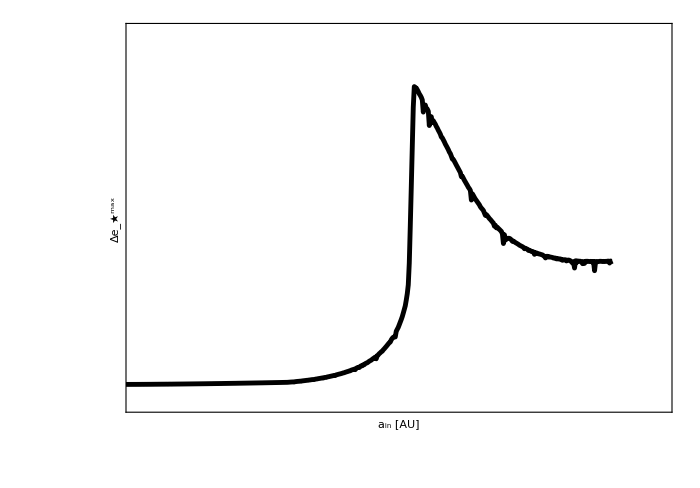

```mathematica
s[j_]:=Table[{j i,j i,{0,0.02}},{i,-100,100}];p[j_]:=Table[{j i/5,"",{0,0.01}},{i,-99,99}];ticks[j_]:=ArrayFlatten[{{s[j]},{p[j]}}];
F1=ListPlot[{Table[{AINSS[[i]],E2MAXS[[i]]},{i,1,Length[AINSS]}]},InterpolationOrder->1,Frame-> True,FrameLabel->{{"Δe_★^max",""},{"a_in [AU]","f_GW [mHz]"}},LabelStyle-> Directive[35],ImageSize->700,PlotRange->{{0.01,0.084},{-0.05,0.9}},FrameStyle->Directive[Thickness[0.005],Black],AspectRatio->0.7,ImagePadding->{{120,10},{105,0}},PlotStyle-> Directive[Thickness[0.005],Black],Joined->True,FrameTicks->{{ticks[0.2],Automatic},{ticks[0.02],  {{0.017587656768848672,5},{0.051426620365713153,1},{0.08163467126770214,0.5},{0.11475558061391707,0.3},{0.15037235016568415,0.2},{0.23870125866677605,0.1}}             }}]
```